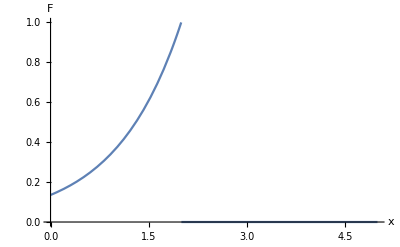

```mathematica
Plot[Abs[Exp[100I (x-2)]Exp[-1(2-x)]HeavisideTheta[2-x]],{x,0,5},AxesLabel->{"x","F"}]
```

```mathematica
Subscript[w, ab]=300;
Subscript[w, bc]=100;
Subscript[Γ, a]=1;Subscript[Γ, b]=1;
```

```mathematica
Integrate[-Exp[I q 1]/((I(k+q-Subscript[w, ab])-Subscript[Γ, a]/2)(I(q-Subscript[w, bc])-Subscript[Γ, b]/2)),{q,-Infinity,Infinity}]
```

ConditionalExpression[(4 ⅈ ⅇ^((1/2+300 ⅈ)-ⅈ k) π)/(400-2 k),Im[k]<-1/2]

```mathematica
Integrate[- (Exp[I(Subscript[v, k]-Subscript[w, ab])t-Subscript[Γ, a] t/2]-Exp[-Subscript[Γ, b]t/2])/(I(Subscript[v, k]-Subscript[w, ab])-1/2(Subscript[Γ, a]-Subscript[Γ, b])),{t,0,T}]//Simplify
```

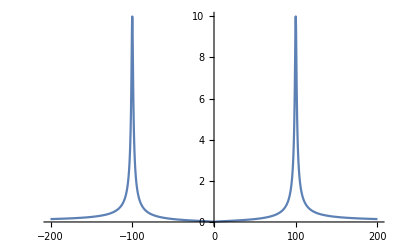

```mathematica
Plot[Abs[(√Abs[k])/(I(Abs[k]-100)-1)],{k,-200,200},PlotRange->All]
```

```mathematica
fx=1/Sqrt[2π] Integrate[Sqrt[Abs[k]]/(I (Abs[k]-100)-1) E^(-I k x),{k,-∞,∞},GenerateConditions->False]
```

-1/(√20002 √(-ⅈ x) √(ⅈ x))ⅇ^((-1-100 ⅈ) x) (ⅈ √10001 ⅇ^((1+100 ⅈ) x) √(-ⅈ x)+ⅈ √10001 ⅇ^((1+100 ⅈ) x) √(ⅈ x)+(1+100 ⅈ) ⅇ^((2+200 ⅈ) x) √((-100-ⅈ) π) √(-ⅈ x) √(ⅈ x)-(1+100 ⅈ) ⅇ^((2+200 ⅈ) x) √((-100-ⅈ) π) √(-ⅈ x) √(ⅈ x) Erf[(√10001 √(-ⅈ x))/(√(-100-ⅈ))]+√((1000100-10001 ⅈ) π) √(-ⅈ x) √(ⅈ x) Erfc[√(-100+ⅈ) √(ⅈ x)])

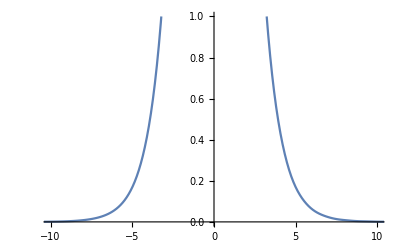

```mathematica
Plot[Abs[fx], {x,-200,200},PlotRange->{{-10,10},{0,1}}]
```

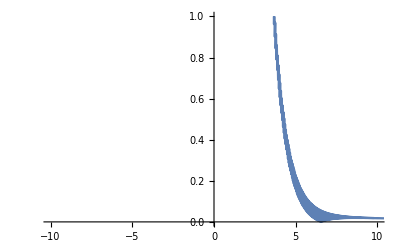

```mathematica
f[k_]:=(√Abs[k])/(I(Abs[k]-100)-1);
sampling=Array[f,100000,{0,200}];
ListLinePlot[Abs[InverseFourier[sampling]],PlotRange->{{-10,10},{0,1}}, DataRange->{0,800Pi}]
```

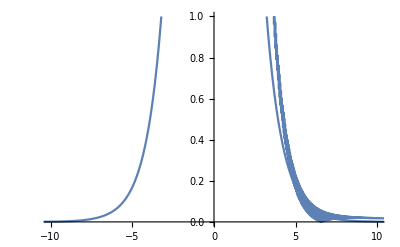

```mathematica
Show[Out[94],Out[78]]
```

```mathematica
Subscript[w, ab]=300;
Subscript[w, bc]=100;
Subscript[Γ, a]=1;Subscript[Γ, b]=1;
f[k_,q_]:=(-√(Abs[k]Abs[q]))/((I(Abs[q]+Abs[k]-Subscript[w, ab])-0.5 Subscript[Γ, a])(I(Abs[q]-Subscript[w, bc])-0.5 Subscript[Γ, b]));
Plot3D[Abs[f[k,q]],{k,-1000,1000},{q,-300,300},PlotRange->All,AxesLabel->{k,q}]
```

```mathematica
sampling=Array[f,{3600,1200},{{-600,600},{-200,200}}];
Dimensions[sampling]
```

{3600,1200}

```mathematica
ListPlot3D[Abs[InverseFourier[sampling]],PlotRange->All,AxesLabel->{x1,x2}]
```

```mathematica
Integrate[Exp[I x]/(x+I),{x,-Infinity, Infinity}]
```

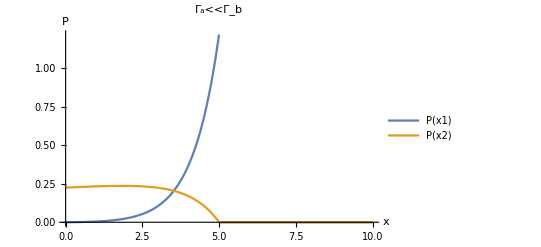

```mathematica
Subscript[Γ, a]=1;Subscript[Γ, b]=0.05;ct=5;
norm1 = 1/Integrate[ⅇ^(-Subscript[Γ, a](ct-Abs[x1])) (1-ⅇ^(-Subscript[Γ, b]Abs[x1]))/Subscript[Γ, b] HeavisideTheta[ct-Abs[x1]],{x1,0,ct}];
norm2 = 1/Integrate[ⅇ^(Subscript[Γ, b] Abs[x2]-Subscript[Γ, a] ct)(ⅇ^((Subscript[Γ, a]-Subscript[Γ, b])ct)-ⅇ^((Subscript[Γ, a]-Subscript[Γ, b])Abs[x2]))/(Subscript[Γ, a]-Subscript[Γ, b]),{x2,0,ct}];
Plot[{norm1*ⅇ^(-Subscript[Γ, a](ct-Abs[x1])) (1-ⅇ^(-Subscript[Γ, b]Abs[x1]))/Subscript[Γ, b] HeavisideTheta[ct-Abs[x1]],norm2*ⅇ^(Subscript[Γ, b] Abs[x1]-Subscript[Γ, a] ct)(ⅇ^((Subscript[Γ, a]-Subscript[Γ, b])ct)-ⅇ^((Subscript[Γ, a]-Subscript[Γ, b])Abs[x1]))/(Subscript[Γ, a]-Subscript[Γ, b])HeavisideTheta[ct-Abs[x1]]},{x1,0,10},PlotLegends->{"P(x1)","P(x2)"},PlotRange->All,PlotLabel->Style["Γ_a<<Γ_b","Section",FontSize->16],AxesLabel->{Style["x",16],Style["P",16]},FormatType->StandardForm]
```

```mathematica
Quit[]
```

```mathematica
f[x1_, x2_]:=Exp[(-I Subscript[ω, ac]-1/2 Subscript[Γ, a])(ct-Abs[x1])]HeavisideTheta[ct-Abs[x1]]Exp[(-I Subscript[ω, bc]-1/2 Subscript[Γ, b])(Abs[x1]-Abs[x2])]HeavisideTheta[Abs[x1]-Abs[x2]]
P[x1_, x2_]:=Exp[(-Subscript[Γ, a])(ct-Abs[x1])]HeavisideTheta[ct-Abs[x1]]Exp[(-Subscript[Γ, b])(Abs[x1]-Abs[x2])]HeavisideTheta[Abs[x1]-Abs[x2]]
```

```mathematica
Integrate[Integrate[Exp[(-Subscript[Γ, a])(ct-x1)]Exp[(-Subscript[Γ, b])(x1-x2)],{x2,0,x1}],{x1,0,ct}]
```

((1-ⅇ^(-ct Γ_b)) Γ_a+(-1+ⅇ^(-ct Γ_a)) Γ_b)/(Γ_a (Γ_a-Γ_b) Γ_b)

```mathematica
Plot3D[((1-ⅇ^(-ct Subscript[Γ, b])) Subscript[Γ, a]+(-1+ⅇ^(-ct Subscript[Γ, a])) Subscript[Γ, b])/(Subscript[Γ, a] (Subscript[Γ, a]-Subscript[Γ, b]) Subscript[Γ, b])/.ct->1,{Subscript[Γ, a],0,100},{Subscript[Γ, b],0,100}]
```

Power::infy: Infinite expression 1/0. encountered.

-Graphics3D-

```mathematica
A=2Integrate[Exp[-Subscript[Γ, a](ct-x1)] (1-Exp[-Subscript[Γ, b]x1])/Subscript[Γ, b] x1^2,{x1,0,ct}]//Simplify
```

(2 ((2-2 ⅇ^(-ct Γ_a)+ct Γ_a (-2+ct Γ_a))/Γ_a^3-(-2 ⅇ^(-ct Γ_a)+ⅇ^(-ct Γ_b) (2+ct (Γ_a-Γ_b) (-2+ct Γ_a-ct Γ_b)))/(Γ_a-Γ_b)^3))/Γ_b

```mathematica
B=2Integrate[Exp[Subscript[Γ, b] x2-Subscript[Γ, a] ct] (Exp[(Subscript[Γ, a]-Subscript[Γ, b])ct]-Exp[(Subscript[Γ, a]-Subscript[Γ, b])x2])/(Subscript[Γ, a]-Subscript[Γ, b])x2^2,{x2,0,ct}]//Simplify
```

(2 (-(2-2 ⅇ^(-ct Γ_a)+ct Γ_a (-2+ct Γ_a))/Γ_a^3+(2-2 ⅇ^(-ct Γ_b)+ct Γ_b (-2+ct Γ_b))/Γ_b^3))/(Γ_a-Γ_b)

```mathematica
Unprotect[C]
```

{C}

```mathematica
C=Integrate[Integrate[P[x1,x2]x2 x1,{x2,-x1,x1}],{x1,-ct,ct},Assumptions->ct∈Reals]
```

0

```mathematica
P[k_,q_]:=1/(((k+q-Subscript[ω, ac])^2+1/4 Subscript[Γ, a]^2)((q-Subscript[ω, bc])^2+1/4 Subscript[Γ, b]^2))
```

```mathematica
Integrate[Integrate[P[k,q],{k,0,Infinity}],{q,0,Infinity}]
```

∫_0^∞ ConditionalExpression[(4 ⅈ (Log[2 q-ⅈ Γ_a-2 ω_ac]-Log[2 q+ⅈ Γ_a-2 ω_ac]))/(Γ_a (Γ_b^2+4 (q-ω_bc)^2)),(2 Im[q-ω_ac]≠Re[Γ_a]||Im[Γ_a]+2 Re[q-ω_ac]≥0)&&(2 Im[-q+ω_ac]≠Re[Γ_a]||Im[Γ_a]≤2 Re[q-ω_ac])]ⅆq

```mathematica
Integrate[1/((q-wbc)^2+1/4 Subscript[Γ, b]^2),{q,-Infinity,Infinity},Assumptions->{{wbc,Subscript[Γ, b]}∈Reals}]
```

ConditionalExpression[(2 π)/Abs[Γ_b],Γ_b≠0]

```mathematica
Integrate[(q^2+k^2)/(((k+q-Subscript[ω, ac])^2+1/4 Subscript[Γ, a]^2)((q-Subscript[ω, bc])^2+1/4 Subscript[Γ, b]^2)),{q,-Infinity,Infinity},Assumptions->{{Subscript[ω, ac],Subscript[ω, bc],k}∈Reals,Subscript[Γ, a]>0,Subscript[Γ, b]>0}]
```

(2 π (Γ_a^2 Γ_b+4 Γ_b (2 k^2-2 k ω_ac+ω_ac^2)+Γ_a (Γ_b^2+4 (k^2+ω_bc^2))))/(Γ_a Γ_b (Γ_a+Γ_b-2 ⅈ (k-ω_ac+ω_bc)) (Γ_a+Γ_b+2 ⅈ (k-ω_ac+ω_bc)))

```mathematica
Integrate[(2 π (Subscript[Γ, a]^2 Subscript[Γ, b]+4 Subscript[Γ, b] (2 k^2-2 k Subscript[ω, ac]+Subscript[ω, ac]^2)+Subscript[Γ, a] (Subscript[Γ, b]^2+4 (k^2+Subscript[ω, bc]^2))))/(Subscript[Γ, a] Subscript[Γ, b] (Subscript[Γ, a]+Subscript[Γ, b]-2 ⅈ (k-Subscript[ω, ac]+Subscript[ω, bc])) (Subscript[Γ, a]+Subscript[Γ, b]+2 ⅈ (k-Subscript[ω, ac]+Subscript[ω, bc]))),{k,0,Infinity},Assumptions->{{Subscript[ω, ac],Subscript[ω, bc]}∈Reals,Subscript[Γ, a]>0,Subscript[Γ, b]>0}]
```

Integrate[(2 π (Γ_a^2 Γ_b+4 Γ_b (2 k^2-2 k ω_ac+ω_ac^2)+Γ_a (Γ_b^2+4 (k^2+ω_bc^2))))/(Γ_a Γ_b (Γ_a+Γ_b-2 ⅈ (k-ω_ac+ω_bc)) (Γ_a+Γ_b+2 ⅈ (k-ω_ac+ω_bc))),{k,0,∞},Assumptions→{(ω_ac|ω_bc)∈Reals,Γ_a>0,Γ_b>0}]

```mathematica
Integrate[1/((Subscript[Γ, a]+Subscript[Γ, b]-2 ⅈ (k-Subscript[ω, ab])) (Subscript[Γ, a]+Subscript[Γ, b]+2 ⅈ (k-Subscript[ω, ab]))),{k,-Infinity,Infinity},Assumptions->{Subscript[Γ, a]>0,Subscript[Γ, b]>0,Subscript[ω, ab]>0}]
```

π/(2 (Γ_a+Γ_b))

```mathematica
Integrate[k^4/((k-w)^2+Γ^2/4),{k,0,cut},Assumptions->{w>0, Γ>0}]
```

```mathematica
S
```

```mathematica
Series[1/(8 Γ)(4 cut (cut+4 w) Γ+(2 ⅈ w-Γ)^3 Log[1-(2 cut)/(2 w+ⅈ Γ)]-(2 ⅈ w+Γ)^3 Log[1-(2 ⅈ cut)/(2 ⅈ w+Γ)]),{Γ,0,1}]
```

(cut^2/2+2 cut w-(cut w^2)/(cut-w)+3 w^2 Log[1-cut/w])+O[Γ]^2

```mathematica
Series[%, {w,0,1}]
```

(cut^2/2+2 cut w+O[w]^2)+O[Γ]^2

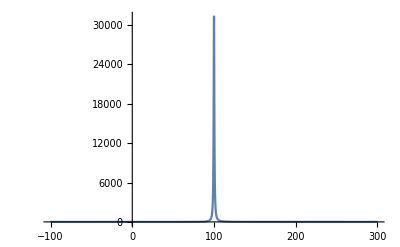

```mathematica
Plot[Exp[-a Abs[(k-wbc)]] (k^2 Subscript[Γ, b]/4Pi)/((k-wbc)^2+Subscript[Γ, b]^2/4)/.{a->0.00001,wbc->100, Subscript[Γ, b]->1},{k,-100,300},PlotRange->All]
```

```mathematica
2Integrate[Exp[-a (k-wbc)^2] (k^2 Subscript[Γ, b]/4Pi)/((k-wbc)^2+Subscript[Γ, b]^2/4),{k,-Infinity,Infinity},Assumptions->{wbc>0,Subscript[Γ, b]>0, a>0 }]
```

2 Integrate[(ⅇ^(-a (k-wbc)^2) k^2 π Γ_b)/(4 ((k-wbc)^2+Γ_b^2/4)),{k,-∞,∞},Assumptions→{wbc>0,Γ_b>0,a>0}]

```mathematica
Limit[Out[18],a->0]
```

DirectedInfinity[Γ_b]

```mathematica
Integrate[Integrate[1/(((k+q-Subscript[ω, ac])^2+1/4 Subscript[Γ, a]^2)((q-Subscript[ω, bc])^2+1/4 Subscript[Γ, b]^2)),{q,-Infinity,Infinity},Assumptions->{{Subscript[ω, ac],Subscript[ω, bc],k}∈Reals,Subscript[Γ, a]>0,Subscript[Γ, b]>0}],{k,-Infinity,Infinity},Assumptions->{{Subscript[ω, ac],Subscript[ω, bc]}∈Reals,Subscript[Γ, a]>0,Subscript[Γ, b]>0}]
```

(4 π^2)/(Γ_a Γ_b)